```mathematica
Clear[L];L[n_]:=L[n]=Ceiling[(n+5)/6]+
Sum[B[2i-1,n+2-6i],{i,1,Floor[(2+n)/6]}]+
Sum[B[2i,n-6i],{i,1,Floor[(n)/6]}]
```

```mathematica
Clear[B];B[m_,n_]:=B[m,n]=If[m==1,
L[n],
If[n==0,
1,
If[EvenQ[m],
B[m-1,n+1]
,
If[Mod[m,3]==0,
B[m-1,n+1]-1
,
B[m-1,n+1]-B[Ceiling[m/6],n]
]
]
]
]
```

```mathematica
Clear[S];S[n_]:=Sum[L[k],{k,n}]
```

```mathematica
L[3]
```

2

```mathematica
L[1]
```

1

```mathematica
Table[S[k],{k,100}]
```

{1,3,5,8,11,16,22,30,39,51,66,86,110,141,181,233,297,378,483,620,792,1007,1282,1641,2098,2671,3399,4343,5554,7081,9014,11507,14718,18789,23934,30533,39038,49878,63593,81100,103631,132453,169006,215536,275268,351827,449188,572976,731471,934729,1193861,1523346,1944273,2483825,3172999,4050018,5168740,6601236,8433052,10766905,13741687,17546237,22413474,28621901,36534123,46642485,59573238,76082647,97128502,123994831,158348756,202237385,258213065,329637335,420919181,537569872,686425664,876335113,1118920912,1428935286,1824720143,2329694413,2974481489,3798375796,4850554293,6193267872,7907312842,10096990915,12893876811,16463901811,21020732864,26840688968,34274909387,43766231642,55881108930,71351143903,91111240551,116343262884,148552113159,189675590347}

```mathematica
Table[N[L[k]/2^(k+2)],{k,100}]
```

{0.125,0.125,0.0625,0.046875,0.0234375,0.0195313,0.0117188,0.0078125,0.00439453,0.00292969,0.00183105,0.0012207,0.000732422,0.000473022,0.000305176,0.000198364,0.00012207,0.0000772476,0.0000500679,0.0000326633,0.000020504,0.000012815,8.19564×10^-6,5.34952×10^-6,3.40492×10^-6,2.13459×10^-6,1.35601×10^-6,8.79169×10^-7,5.63916×10^-7,3.55532×10^-7,2.25031×10^-7,1.45112×10^-7,9.34524×10^-8,5.92408×10^-8,3.74348×10^-8,2.4007×10^-8,1.54705×10^-8,9.85892×10^-9,6.23686×10^-9,3.98063×10^-9,2.56148×10^-9,1.63834×10^-9,1.0389×10^-9,6.61231×10^-10,4.24421×10^-10,2.71992×10^-10,1.72948×10^-10,1.09946×10^-10,7.03859×10^-11,4.51323×10^-11,2.87694×10^-11,1.82901×10^-11,1.16831×10^-11,7.48779×10^-12,4.78211×10^-12,3.04277×10^-12,1.94067×10^-12,1.24249×10^-12,7.94424×10^-13,5.06074×10^-13,3.22527×10^-13,2.06245×10^-13,1.31927×10^-13,8.41399×10^-14,5.36153×10^-14,3.42485×10^-14,2.19055×10^-14,1.3984×10^-14,8.91327×10^-15,5.68917×10^-15,3.63736×10^-15,2.32344×10^-15,1.48166×10^-15,9.45292×10^-16,6.04053×10^-16,3.85965×10^-16,2.46261×10^-16,1.57089×10^-16,1.00331×10^-16,6.41095×10^-17,4.09232×10^-17,2.61066×10^-17,1.66674×10^-17,1.06486×10^-17,6.79954×10^-18,4.33854×10^-18,2.76919×10^-18,1.76881×10^-18,1.12965×10^-18,7.20961×10^-19,4.60122×10^-19,2.93833×10^-19,1.87666×10^-19,1.19797×10^-19,7.64556×10^-20,4.88148×10^-20,3.11759×10^-20,1.99046×10^-20,1.27042×10^-20,8.11018×10^-21}

```mathematica
Table[L[k],{k,100}]//Accumulate
```

{1,3,5,8,11,16,22,30,39,51,66,86,110,141,181,233,297,378,483,620,792,1007,1282,1641,2098,2671,3399,4343,5554,7081,9014,11507,14718,18789,23934,30533,39038,49878,63593,81100,103631,132453,169006,215536,275268,351827,449188,572976,731471,934729,1193861,1523346,1944273,2483825,3172999,4050018,5168740,6601236,8433052,10766905,13741687,17546237,22413474,28621901,36534123,46642485,59573238,76082647,97128502,123994831,158348756,202237385,258213065,329637335,420919181,537569872,686425664,876335113,1118920912,1428935286,1824720143,2329694413,2974481489,3798375796,4850554293,6193267872,7907312842,10096990915,12893876811,16463901811,21020732864,26840688968,34274909387,43766231642,55881108930,71351143903,91111240551,116343262884,148552113159,189675590347}

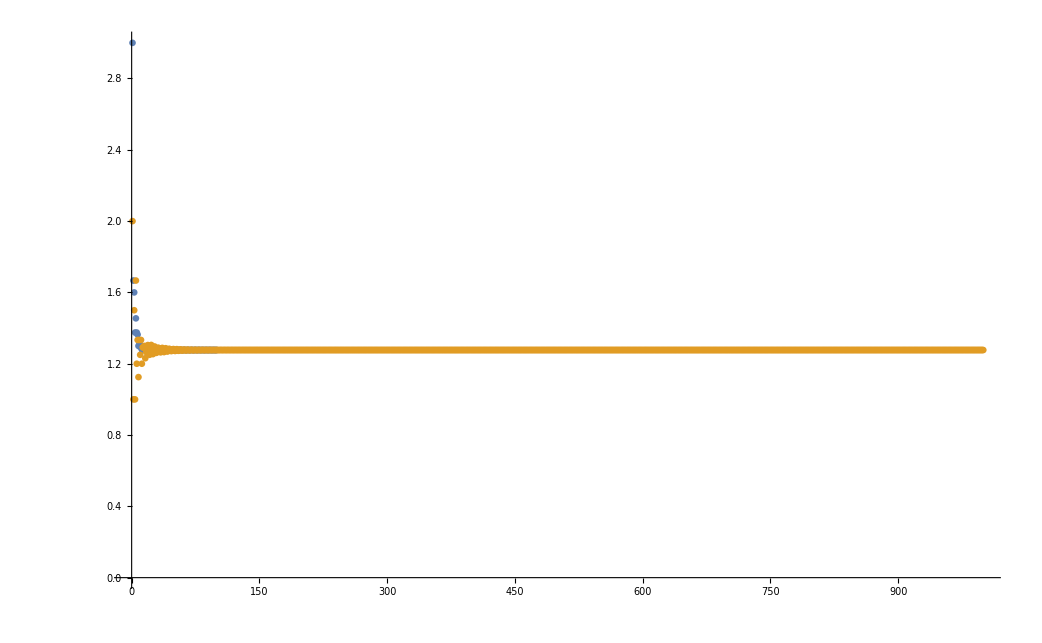

```mathematica
ListPlot[{Table[N[S[k+1]/S[k],50],{k,100}],Table[N[L[k+1]/L[k],50],{k,1000}]}, PlotRange->All]
```

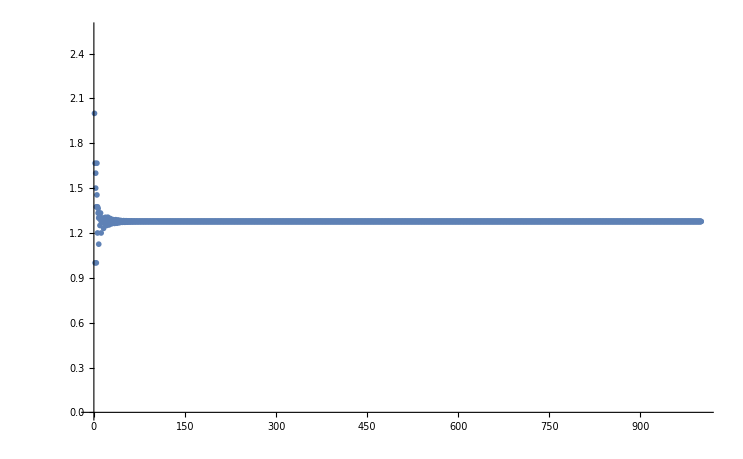

```mathematica
Show[{
ListPlot[Table[N[S[k+1]/S[k],50],{k,1000}]],
ListPlot[Table[N[L[k+1]/L[k],50],{k,1000}]]}]
```

```mathematica
Table[N[L[k+1]/L[k],50],{k,2000}]
```

{2.,1.,1.5,1.,1.6666666666666666666666666666666666666666666666667,1.2,1.3333333333333333333333333333333333333333333333333,1.125,1.3333333333333333333333333333333333333333333333333,1.25,1.3333333333333333333333333333333333333333333333333,1.2,1.2916666666666666666666666666666666666666666666667,1.2903225806451612903225806451612903225806451612903,1.3,1.2307692307692307692307692307692307692307692307692,1.265625,1.2962962962962962962962962962962962962962962962963,1.3047619047619047619047619047619047619047619047619,1.2554744525547445255474452554744525547445255474453,1.25,1.2790697674418604651162790697674418604651162790698,1.3054545454545454545454545454545454545454545454545,1.2729805013927576601671309192200557103064066852368,1.2538293216630196936542669584245076586433260393873,1.2705061082024432809773123909249563699825479930192,1.2967032967032967032967032967032967032967032967033,1.2828389830508474576271186440677966101694915254237,1.2609413707679603633360858794384805945499587118084,1.2658808120497707924034053700065487884741322855272,1.2897051215726849456802897051215726849456802897051,1.2880064179703168872843963096670677898114721219414,1.2678293366552475864216754905014014325755216443476,1.2638172439204126750184229918938835666912306558585,1.2826044703595724003887269193391642371234207968902,1.2888316411577511744203667222306410062130625852402,1.2745443856554967666078777189888300999412110523222,1.2652214022140221402214022140221402214022140221402,1.2764855997083485235144002916514764855997083485235,1.2869709259153481464557034329125492660078825612612,1.2792153033598153654964271448226887399582797035196,1.2682326000971480119353271806259107626118936923184,1.2729461330123382485705687631658140234727655732772,1.2837309262841177734794756071351816032667096496884,1.2817082970602022366570682381303154088260898680774,1.2717120129573270288274402748207264985174832482138,1.2714331200377974753751502141514569488809687657276,1.2803745112611884835363686302387953598087052056742,1.2824253131013596643427237452285561058708476608095,1.2748920091706107508683545051117299196095602633107,1.2714948366083694796474383711776237593195745797509,1.2775300848293549023476030775300848293549023476031,1.2818184625837734333981901849964483152660675128942,1.2773078405788506019809026748116956289662534843722,1.2725654188927614796843757889879769114911473735225,1.2755960817268497033701664388114738677269249582962,1.2804753996077667195246003922332804753996077667195,1.2787581954853626118327730059979225072879784655594,1.2740651899535761233661022722806220712123925110382,1.2746226947455559540382363413634020651686288725125,1.2789340529827059596299829701806720626923250174298,1.2793200247072584142671275183661668265629312270834,1.2755546935561181836840901727201695746477929880957,1.2744326380901313649979294272124001780161061731095,1.2775629905227633906126496450680984431427732942781,1.2792134868141841378454788223848730387772024785025,1.2767554217453538861967280637098241687858394634868,1.2747794303236415064888149539453532225169295884547,1.2765615367016450507712801404362046588271182140141,1.2786981429431613079702850359645338966853268267503,1.2775433665876606530403731160267713223452633141628,1.2754027928281833547363714642350755590929942240848,1.275987536015641078411195719283803251697880222268,1.2780228065334094419165922171833187794568988944514,1.2779177471936752900461719409136401557873840544373,1.2760815278839625562098041922443476995777076022636,1.2757948242954496523722771902621028008100618617514,1.2773761404573397503775602023888763955078401601808,1.277957635104600661310763702206657200077899036456,1.2766661490347541111109899697747563150088002048576,1.2758807242592406712518564094532803209295094380026,1.2768711483062295431408812175717388531498842505382,1.2777773278445798128869444027131834137444777196496,1.2770794603876295506433205636897306537645489520296,1.276127180728727627666011882012449072127350270303,1.27655294234571824494820276186392839034511618654,1.2774916127200559971305770349770928122148393807894,1.2773046095164510513870410392514352040095530517741,1.2764285468726894391690264363934566460411654920083,1.2764143256699883054040237813460690051190117716262,1.2771937419467019243910511509587011234756874801345,1.2773670945542925352620494609833572724142319407432,1.2767071353900893801303364341368743589306805028698,1.2764161791701803301588562488441185058045424040868,1.2769452471733529621534206991795986567817062316744,1.2773142841944110451753404707703759371455947128065,1.2769179616109739991186707074247706888037686484498,1.2765068867617191641774693414940233201481131552072,1.2767756947822317137956269381304390567849910625225,1.2771983159129933640668868431389027121876462466615,1.2770453897027888865946362328868822026555173202605,1.2766366833753609848098924244332491723680488951092,1.2766887406577296072644239506988251133999619998236,1.2770644484108063183927890143906417947872694688465,1.2770954286653129202389233791907286471841885828069,1.2767664610300869762522772961407746612047805692783,1.2766708871821158692368737542062585886829765140117,1.2769448597584116222242711083887379273231065973104,1.277086718693340232727777874604826619426224586711,1.2768713900845852598729520951418524528451100208605,1.276700333686476591019923197869249195686799157321,1.2768572388617359052213844434995853434363236731856,1.2770423566077392273624245781801749732048317885738,1.2769404490491953962787193040321313333776851457712,1.2767541861458906743964078662022225904527347209468,1.2768066988813009208996333723283818750013601102665,1.2769838430952585361668030719111003431101543236503,1.2769734974538992323350712444344582760203924332236,1.27681323300537927843219327347233357206365502548,1.276789386422744878017360528257890128897767438923,1.2769275464560621402403916265388679329621963991884,1.2769773421214541846242811516984351846941698320469,1.2768642760086248833124807300946676729947114388778,1.2767964916440941323313136138597081671170650519623,1.2768834382765344130290215611890755182493365587535,1.2769618995622068145919121764724597856391522358642,1.2769004630293973485857623569306357278305319481713,1.2768177457720519348666074848005305103017284871716,1.2768555171547197531709535881935854907589363623523,1.2769371623198833022018546490906985587987799215048,1.2769202849289333602322824638802045445535147622684,1.2768439182229293500943173646088432061309918352222,1.2768432231613458572741459220776305615028372222147,1.2769112579237830943561614733491115184654708065514,1.2769259160503416123770883944326405065490456083882,1.2768682041272211489801825388013840933809119509239,1.2768432086922360433312079500214888610953938488347,1.2768895722784165110593948033186969631731871188759,1.276921454776653879728226257963419254385363726376,1.2768866421386674982372748422753607129111651027327,1.276850996598471605494259731616057513139264817491,1.2768747183830425169763443953553780965730221814424,1.2769114369805160912887039032736578375858037443732,1.2768978354423915566223765140416782202457996348248,1.2768622494363874831255577665342625957578391620076,1.2768670478224922095585716173043115917332929404934,1.276899807821958704464347026967604132725211664932,1.2769022837480929191260021723607807396399886597199,1.2768735487812417274804976296518675199987578350288,1.2768654085570946729732165702026364829785855605796,1.2768893817664693404486303214536609657141270044853,1.2769015959105915222759870135101787828524074814969,1.2768827143399427031368813980765777408709238927222,1.2768679141030735740616262921494268624656033750342,1.2768817161390072522836438147984340617790309638351,1.2768977772985095788105831070610608869029969407921,1.2768887696937635067825485667750934485708468032874,1.2768725726721912536866562991247864724901696250386,1.2768772715753192625503654781226937328355212126817,1.2768927011682602996474439323024745873986074609142,1.2768916900839042448283501342848229699462268503539,1.2768777069033756593498178822925395453314128477479,1.2768757239426563871274634491023425122113543911797,1.2768877981760097069363898239181212002929005335013,1.2768920600062137812121893117091564301162461120264,1.2768821602783920477441899369487754171070637756351,1.2768763127105714482772963572019802323058073235729,1.2768839439054844099084889259361934144553247047961,1.2768907390558253893267691796077979868014725913081,1.2768853285345525562914657283249531708924243999722,1.2768781457699864365124547570440982480662147533918,1.2768814937191859493522233242959231194218599983997,1.2768885969880479368120687930227175065251967495016,1.2768870738921555033013634531002726835900144424823,1.2768804182344430660837987726098321989546732058375,1.2768804045073409800156142655474758509831869313081,1.2768863434806583537450677947447679280303658190358,1.2768875812628658091931084549265979704529832537507,1.2768825347191543680811414851892068827197441471184,1.2768803883129209008092968021385933083207789277901,1.2768844506507405771070089832534628136522523311596,1.2768872051297732283622130217097347251505353644733,1.2768841469031042061033477263935148937180692741031,1.2768810567887556583388603864765163841391411542275,1.2768831493250359207065797971431245133788752882229,1.2768863398169146794147428200481660220931788147405,1.2768851300880717336160513484594966241338799822135,1.2768820321739197070502763371188254045068383545721,1.276882472870965494834594848950566946744911799157,1.2768853294559411849719385959014884471972233446851,1.276885525495165163129899598968814105776150622675,1.2768830157571895116235063260136157457225238874875,1.2768823228440759606323050152679877997454999811488,1.2768844204076285208323173363950243892186461541994,1.2768854718447281995793196952507162624188612492568,1.2768838162298968694425317548837420322949913034891,1.276882535923102832502202951555591788022967994852,1.2768837497603737135025132321666964973785688129916,1.2768851432284888345517593597521172700967366833535,1.2768843471326389976039533752232149717141731837261,1.2768829388473730842132168941352911730114589878459,1.276883358946559019533666157251469171140557408121,1.2768847028737550196356274283375711409400595812776,1.2768846051591983878190232088636541489264870618222,1.276883385215321933299834267343476360990350862057,1.2768832207062078027851909148765040409304290928649,1.2768842758548406460455926227328272224742745178449,1.2768846404547828934575535060724552919101366527947,1.2768837737161280393507211779463405149629385759983,1.2768832693659487459747111771966154464911012079695,1.2768839390645301220499639963290927238449671194717,1.2768845275157150049505915197759712917818716667678,1.2768840510772770053050107193904278877564992169352,1.2768834274265199437383376835170156007961456531931,1.2768837240690737031032631834294318880586774657571,1.2768843420427468873958773016114088656379925587902,1.2768842047394359945166867049158701722536690649594,1.2768836247150523619060525434231327542118972779214,1.2768836276000086517555370270829430444539570490409,1.2768841460078396748397908562597306209730611889518,1.2768842504086132318375643387884364246755439472637,1.2768838091477014748004718153508280928460699380226,1.276883624887985242458606736394147672707997964679,1.2768839807972560395899924430020617595460238708091,1.2768842187376523367236830670293234790081284023979,1.2768839501026481124749770870219395655242929344926,1.2768836822488691672527121329372038456274888200795,1.2768838667975069904113224347448389411716203140733,1.2768841440046620367505155340146569104302378330138,1.2768840364534695079862766078908682850737699841487,1.2768837667851456173257183373082501417458615071759,1.2768838071530117352156530884654526378159999940809,1.2768840562275391981324298819882479584103665390008,1.2768840715873434580433492868803704399419277210042,1.2768838523975548368565636060336872722648566592801,1.2768837934541331532754775339579464823478313453898,1.2768839769708473831386857370435251128431058588663,1.2768840674618558935215664586076697544550403625272,1.2768839223020299764384109264613983418525376448287,1.276883811562323500119250433748831710050265340522,1.2768839183008752933131503327596198172460641316574,1.2768840391890269049021865594927803567837507676024,1.276883968844937864643244271340943484605348612109,1.276883846407069095272127419644050579304663540126,1.2768838839404578086293284383833759913108674045267,1.2768840009911737908285917703827081190872550724576,1.2768839916375970370183165475592562682511232150859,1.2768838852113022670804408812876902208546600836614,1.2768838715999609329611564539756239645769271315504,1.2768839638024528419941266949744532952343265671783,1.2768839949803806285896624165068689978094270975945,1.2768839191010488196917960206932158043157079943576,1.2768838756090599812027153699099518705742990533458,1.2768839343749364196981497835247151199446875161245,1.276883985328753780040652939751508609217174788325,1.2768839433805708598845186078599001296927935851193,1.2768838892356941037280639193627536532495751910354,1.2768839155115101296227653995610409285813408548423,1.2768839692711040271171697255325264716523946243152,1.2768839569071641433518046796836762252553013916676,1.2768839063623275252099936311442438735226275707029,1.2768839069699251838220284254242684092772208709816,1.2768839522188265480467118981689706284300280247248,1.2768839610137654162245394639073822989413298352781,1.2768839224330383445495983097595509246826689967054,1.2768839066200710438828551973863714115097533737542,1.2768839377996263887976216262433697842846436251626,1.2768839583506114998415495600449629762218745696164,1.2768839347561123502319849592284593471204297929561,1.2768839115405179705028792167109863494228379745231,1.2768839278136575583896503966999896459894643787071,1.2768839518972584662622921806389545556993499194363,1.2768839423393240330979137195758871612489833359961,1.2768839188665385835934328235331638739154492895246,1.2768839225555689181292105858771367122393647674742,1.2768839442719725562672122418352498402468260877961,1.2768839454599217533972049261316025654636938245513,1.2768839263179075526921653269592171974713888023509,1.2768839213073114253832498439905839155866491202964,1.2768839373622343004736291094518232436513020416535,1.2768839451484304897116896910901186746117552048237,1.2768839324222457874995321004058104633392467197878,1.2768839228450578166459765171674254953886962622205,1.2768839322299553198539194991535222901588880433565,1.2768839427165441697094106450145097423058641360805,1.2768839365022152729191087177867548875483813269303,1.2768839258580307361650326024510822294689175776787,1.2768839292093376158510116281649699844272237538054,1.2768839394034138237072487431648212678308300030509,1.2768839385151655291699673784637560271788298366066,1.2768839292311863782316764968306517948442982089383,1.2768839281083614113446024540957538705384605682256,1.2768839361648620084877064499894741777086455347973,1.2768839388297601274388707569904331815307687597741,1.2768839321872972695751777582650048652939761667267,1.2768839284375197655002088594790251494766344241836,1.2768839335937401331843908503272103927955190307062,1.2768839380053409079638920491139085243314531583803,1.2768839343125231953241230611063084985067058902079,1.2768839296120662092937534714512649139623270416755,1.2768839319388351530609480684867523188533568170795,1.2768839366152744416092096760638613008908844897016,1.2768839355030789355565187129514217271861649686319,1.2768839310987154259374773321800577138263129699356,1.2768839311827540721246276892358181091247508693314,1.2768839351320580090220516571669189272527197636441,1.2768839358719944449682461442702029705847600771062,1.2768839324989734370416292605213676025151396246648,1.2768839311423587524767588636293527324560998643719,1.2768839338736524939232025878178089870085896489249,1.2768839356483779346649417246847801641408103518093,1.276883933576260863114359602248193659428063536651,1.2768839315642950761460282154789331679135124371554,1.2768839329989812807547816685377686256704581669539,1.2768839350912041116078052415312251321626956185764,1.2768839342421409616735747390107410776735416097815,1.2768839321991159162018734283586086786220226493644,1.2768839325355207667418887654015786960729758260345,1.2768839344288349159273117465311919613110564996746,1.2768839345192081698844376942809752146309273569606,1.2768839328476153767524159527662236764503563354666,1.2768839324219926695913886419873361928157449382968,1.2768839338264647780897290578782932929604336546341,1.2768839344962570168084952493678151419047511306192,1.2768839333806406410855805864394673684900110818393,1.2768839325524749293235008750105742458972464302876,1.2768839333775362761566996097107211194006847945657,1.2768839342871310234995128640262642028702797512838,1.2768839337382638148238971514779032858811028528859,1.2768839328129681454344944699612713919605115992457,1.2768839331120251586633901660122735220553732158466,1.2768839339997879551942582694884599078336570210464,1.2768839339160019740508284211858739210589170682097,1.2768839331061687662856178311755470473066811682919,1.2768839330138543808428311279150318484057131333393,1.2768839337177772294578737880827588796951913741555,1.2768839339454486750791759317066540909561694153765,1.2768839333640081939191926528319394224928435306593,1.2768839330407726930489987570997386724169024460909,1.2768839334931477849638218350200729252716616347232,1.2768839338750639942295800052139445326885457546853,1.2768839335500201457632673247259095711467225272434,1.2768839331419927054877035695814844429910370008158,1.2768839333479743521379410090446272770610910139597,1.2768839337547432340969141416788114902933081104478,1.2768839336547937530062893057746722702772467779255,1.2768839332710287794620830210382545301947969066969,1.276883933281065836931339701667367419845978553322,1.2768839336257403066467118482319231535344153261816,1.2768839336879053348685643269894578332241545266033,1.2768839333930279262831129743583614905702122771811,1.2768839332766809407898253740642808206348027884058,1.2768839335159216465110974487076236093168835688357,1.2768839336691582131622159230426024479193361652182,1.2768839334871991260494238257247675652895074828314,1.2768839333128500534455149234515864086298027112896,1.2768839334393147249330490397047366758192544290242,1.2768839336210602389955044650641851324205989480613,1.2768839335456640832889613470929189618008295202246,1.2768839333678537307170276729257935014912616212049,1.2768839333984708996523165303883898486441884057759,1.2768839335635277683977323672776015125432041086011,1.2768839335702549459642212424609496661105809031191,1.2768839334242898711569785034948684229810664929127,1.2768839333881635119716921193354416990655721494419,1.2768839335110178445772291936188718923423044385061,1.2768839335686210669294358862327701881778272868142,1.2768839334708305466575369828730567506393563663992,1.2768839333992260778874707784465981366064107463521,1.2768839334717518332786885491738580162144123286474,1.276883933550642280696030485083753618827143072759,1.2768839335021749553689722285094764582692607373462,1.2768839334217445995877507483101808510196344424892,1.276883933448416175323283104117076971118197330733,1.2768839335257235958510658094303441468595503199495,1.2768839335178655746038445235305860889144699920231,1.2768839334472284146741612214375107839985978715587,1.2768839334396672241873749821147736024442526425833,1.2768839335011677176805992966554873211316933136628,1.2768839335206088893164008855622744976679508329804,1.2768839334697165870086211509877487091870172572326,1.2768839334418587129398999447629172319601467125891,1.2768839334815437987582320288394451689881278150137,1.2768839335146029472117014300537815386207510054222,1.2768839334859963313252474667367008010019097482659,1.2768839334505798898784596495490556076825278202106,1.2768839334688098450586940555417415316354001205166,1.2768839335041894590340710094875418959062540803775,1.2768839334952155893386538455191163191210229320668,1.2768839334617788986391391261384936467881268114036,1.2768839334628904015638292577284488082447164317703,1.2768839334929701182112736239915137656476632263702,1.2768839334981849528447530945538037607540901223276,1.2768839334724076249885186709261000959440285361844,1.2768839334624328229130055050534323921956676295676,1.2768839334833869795228615918947275831274921289437,1.2768839334966159175952934095329356347107475893513,1.2768839334806391199396625481634485634334687877627,1.276883933465532182967446432559101246083234882781,1.2768839334766779454715160802109541745082426934428,1.2768839334924645401491749787925446689096687318664,1.2768839334857718988182801367245594354472649272467,1.2768839334702974717404739864865584611769519549354,1.2768839334730790405184779025465604010705376144542,1.2768839334874677103002775933875344963783607075843,1.2768839334879536696560418217388220569736264867422,1.2768839334752085744501904003031909953539874623191,1.2768839334721447151182457361693734718079917297548,1.276883933482890557296333311398150648530432650576,1.2768839334878432600342484721573466721992800068735,1.2768839334792720093827012886293758180991302215116,1.2768839334730817953545394642765550317984665759373,1.276883933479456328448878059763541034730276052567,1.2768839334862980161351467536246883500644438935978,1.2768839334820190212487417380918904503417930535448,1.2768839334750281616166577123703051410679808191958,1.2768839334774055982028364295625751953786749083914,1.2768839334841372325977931771729874352917433063731,1.2768839334834039051431344989392984409633133118855,1.2768839334772429633704727302272717316294714627792,1.2768839334766262905483185076763634653539723541843,1.2768839334819991705891156086854452865009514805445,1.2768839334836584248906817608607814319912221988775,1.2768839334792042235882084896175885493119229821937,1.2768839334768037871654232932975021235005442349754,1.276883933480284897858946167569252833421638411747,1.2768839334831462162161085001220618346010653030714,1.2768839334806289303797263304557909775285950787884,1.2768839334775550539108802297868047082745764113351,1.276883933479168029851326951461313893222198471281,1.2768839334822450564753335077987374886610499182366,1.2768839334814400463795420838880829368112527698565,1.2768839334785269358209821555262968801266107263766,1.2768839334786444655560453578620823984723570116628,1.2768839334812693758135894161784291881546494616737,1.2768839334817061171802902670688933117033869573817,1.2768839334794528725438460447213885849059224596362,1.276883933478598005172726928373522726438760855261,1.2768839334804331654717598865391442843690661631876,1.276883933481575037579684818824618965016740220611,1.2768839334801723439560040719745276759538303661679,1.2768839334788634925043477356925123734032377478115,1.2768839334798456476514837166310730732965965890572,1.2768839334812167881402780308909609010351229942421,1.2768839334806229192212107450601445092681397881665,1.2768839334792762957367614279001884421955984758819,1.2768839334795285842975079116891250954393253313111,1.2768839334807828333648735012059838735052016736839,1.2768839334808164260892570666135160237181876358902,1.2768839334797036368086829581690190824668133687321,1.2768839334794440167686967318099343907842967852842,1.2768839334803838768781043619002450476890109706877,1.2768839334808095961706673977232641376358942515685,1.276883933480058392790060341946084079403496368464,1.2768839334795233200389665369650881784117249502312,1.2768839334800835358501345810085855528424753992096,1.2768839334806768217008448816763944202647318749809,1.2768839334802991211957766958175898535914068387049,1.2768839334796915291128358251045332122400370386512,1.2768839334799033382921038104119097574806153073475,1.2768839334804894695376314590755454509835061942158,1.2768839334804213300139598052373305514039034953919,1.2768839334798840048177556689118431121490477413084,1.2768839334798339557529933526947102469146027692843,1.2768839334803033208325821117770171253534196464788,1.2768839334804448579059619579377833684612935254581,1.2768839334800550427747622080458209614941770725127,1.2768839334798482460602657091381926442920578765711,1.2768839334801535768814250788391068078084027228954,1.2768839334804011998275688358610751685203786228444,1.2768839334801797164574791437482957223682013053576,1.2768839334799129486009775774732088415370953462668,1.2768839334800556271348383649728766180650962957023,1.2768839334803232246389871910241923504398184086921,1.2768839334802510697267305215504403693345101565464,1.2768839334799972845109453845466455998669393021162,1.2768839334800093302397508577472654362150825158324,1.2768839334802383807684725731199233598265748662547,1.2768839334802748929135168050698038255141187414506,1.2768839334800779442819875826859339230736389344421,1.2768839334800047068726866941972961525021085274267,1.2768839334801654183123443144553384356596014026919,1.276883933480263964171992751531000323188006517966,1.276883933480140825752712881758878723803058784782,1.2768839334800274393724366531153329756921663346653,1.2768839334801139723373557346938895814415436417178,1.2768839334802330537362409127078198077558356509977,1.2768839334801803752121665709653022027116469116067,1.2768839334800631956848797580747237533580599353439,1.2768839334800860433759907995848255245669941806757,1.2768839334801953692599841759441906193763559986948,1.2768839334801975321745510931974249591068220133796,1.2768839334801003786515475289463620419926452214037,1.2768839334800783995445403403612877302423138286169,1.2768839334801605971008108907023326004627333623732,1.2768839334801971807144265634331259746745957352961,1.2768839334801313487067957883929101982998622096927,1.276883933480085104154755403905100688519416112789,1.2768839334801343323535852893246844741732862745887,1.2768839334801857753447579094484890623488050113346,1.2768839334801524427975955491785098459520147386465,1.2768839334800996390973979032337799027484340449424,1.2768839334801185001322076007804186039573932062163,1.2768839334801695323162597517066066938914327475755,1.2768839334801632250517845148574659178794668836396,1.2768839334801163649171515258178232777308261064361,1.2768839334801123258245954215937125436516858794481,1.2768839334801533263642354552555215700872112629226,1.2768839334801653929277426580149472059014563199782,1.2768839334801312800112738605117599535242743886883,1.2768839334801134682842094119869799063813477133063,1.2768839334801402467802553981917373547944170146688,1.2768839334801616739591317417794574326125575365141,1.2768839334801421892802432449961945719456230095242,1.2768839334801190395548281270634335938631601685969,1.2768839334801316572765736200294235577312766626952,1.2768839334801549277567088874993125781434407761137,1.2768839334801484653772276371195376280246409370344,1.2768839334801263572840809784783587968869104385453,1.2768839334801275643936588021227742609614361349227,1.2768839334801475503198459970352610503247918060011,1.2768839334801505968913566320720637851347190025954,1.2768839334801333832848667739667594412449966684324,1.276883933480127111355787490365548945617343168402,1.2768839334801411844240613101106717526174048470305,1.2768839334801496876987126517754569214856208755622,1.2768839334801388787729181769807400803815391769548,1.2768839334801290570557981905572153220815275869515,1.2768839334801366798750879840920562715590293932749,1.2768839334801470211505303753701455370153460787465,1.2768839334801423499174390242367491954780687419023,1.2768839334801321538868314218297653524388799424995,1.2768839334801342200858553633784867074984507421783,1.2768839334801437488866593011329993880457629922071,1.276883933480143870625355507466596323600146161557,1.2768839334801353889822712346223384157540988483382,1.2768839334801335300657355036160919391955261992831,1.2768839334801407183902006531271200926186224110436,1.2768839334801438612754153832000132060089391407585,1.27688393348013809250555780258997072658929591627,1.2768839334801340963002138870411555352069553655541,1.2768839334801384216860188495680989688025353201148,1.2768839334801428818359280806723710504951840456935,1.276883933480139940757871987948255038144811170209,1.2768839334801353520847442414694040396524494352327,1.2768839334801370308110736292797011391688085521287,1.2768839334801414737288777996639509004976104669759,1.276883933480140891880026981102823605417082011016,1.2768839334801368054310807145189608983197512036109,1.2768839334801364816102663581280436388737969226476,1.2768839334801400629342657582697890834351201125801,1.2768839334801410910493933640838623496613514199226,1.2768839334801381060069873652224673552971668907613,1.2768839334801365721845546168435509240560474125424,1.2768839334801389205455206665879010032677829254945,1.2768839334801407744514772738311630859860596753098,1.2768839334801390605340854863042291749295184354109,1.2768839334801370517970298331961949151927881532493,1.2768839334801381673694617034212522550206369580069,1.2768839334801401908589232448848731573231484348708,1.2768839334801396124986532739778545172554051615304,1.2768839334801376866958752023629549687318826102626,1.276883933480137805622269376856319530746981709436,1.2768839334801395494092120550362886196863702487011,1.2768839334801398030789197894162051153374816567171,1.2768839334801382986725544745517829396354021799901,1.2768839334801377617680484475660460546912019983477,1.2768839334801389940221113444312506114496954832279,1.2768839334801397276221588126357382316780151073375,1.276883933480138778919239680541116083742713545768,1.2768839334801379282331308199313198477065891440917,1.2768839334801385996365456498384612496175661405694,1.2768839334801394976280184665450823785463230437985,1.2768839334801390835433609062781638359611469729023,1.2768839334801381964195711829126415485553160090026,1.2768839334801383830274704235892733410067640248739,1.2768839334801392135080970986435588152410845791919,1.2768839334801392182897078717411698578019113366293,1.2768839334801384778711476364923216512559610038892,1.276883933480138320812824313125359121594578506869,1.2768839334801389494059938665902218846612262312864,1.2768839334801392193323912213101673963516806114922,1.2768839334801387138614583358603338608205385096117,1.2768839334801383685799180705822785105330672220312,1.276883933480138748584447289926981945766542608441,1.2768839334801391352480139027656283458813758264046,1.2768839334801388757920800132712473831359952501559,1.276883933480138477060911181390127362461236488985,1.276883933480138626407783757132721440682352375141,1.2768839334801390131905824381635678657403305699369,1.276883933480138959677124115160784354191238955336,1.2768839334801386033369116620398725494442502856504,1.2768839334801385775778177996071002349771830268006,1.2768839334801388903823010459817236981297191101173,1.2768839334801389779275188038208382255488151382354,1.2768839334801387167391449017042400192202706005388,1.2768839334801385846861116625786434201299942654827,1.276883933480138790610155323708294124031049051966,1.2768839334801389509930943095499179152614682345762,1.2768839334801388002518988012700252808942033770118,1.2768839334801386259649458371957819929037033610097,1.2768839334801387245729004356461990892349170361511,1.2768839334801389005145658330625532868475165806541,1.276883933480138848789625468382591826364642539357,1.2768839334801386810453044665520796655005654834206,1.2768839334801386926073584936729107890477864782912,1.2768839334801388447457227545339302013637428493785,1.2768839334801388658184026686064562480063786310566,1.2768839334801387343465005405337553023514664799599,1.2768839334801386884040516072834119700865970229364,1.2768839334801387962941084721201558754108184735026,1.2768839334801388595726070848334250162103252941953,1.2768839334801387763124558446604058645621005418429,1.2768839334801387026398514920378340130234327940988,1.2768839334801387617669587516772809803536856429898,1.2768839334801388397388313325734184322028509081907,1.2768839334801388030434942452944727600333547232653,1.2768839334801387258624058242142267218369162848364,1.2768839334801387426951332414718524684546670832894,1.2768839334801388150714927536118487279129683062839,1.2768839334801388149794761738024993481879432537069,1.2768839334801387503470427021692605730125197220788,1.2768839334801387370919199468211816291049167467108,1.2768839334801387920567642192243465990070913541631,1.276883933480138815232482299719982789918383412462,1.2768839334801387709454760786883763395822487321006,1.2768839334801387411166544071706090854452365028681,1.2768839334801387744981960696222681770663632402132,1.276883933480138808016120876859749050332155324933,1.2768839334801387851316172746810304267296501819253,1.2768839334801387504863971011286537966650045157122,1.2768839334801387637671258860156656700463462288116,1.2768839334801387974369369394372001023114334789557,1.2768839334801387925286239777575189762718096694033,1.2768839334801387614572975823438046253228171266847,1.2768839334801387594274119706299766095299361681396,1.2768839334801387867472242253018757609078365931733,1.2768839334801387941969876673618384522272960870874,1.2768839334801387713447337563062129096345623280673,1.2768839334801387599783215866034327861088881992646,1.276883933480138778033973995563262885080755950951,1.2768839334801387919071386017868532147065749788382,1.2768839334801387786508983658522255702390132892901,1.2768839334801387635302355281542889231768289149749,1.2768839334801387722444086456418545377860800555762,1.2768839334801387875414847001758745855345377676231,1.276883933480138782918611379766064989183284041817,1.2768839334801387683083067235687852470245894186743,1.2768839334801387694204223994743919475485466013639,1.2768839334801387826931523187259923327449949841688,1.2768839334801387844392227227751991632024976475662,1.276883933480138772950405428852835582677645054417,1.2768839334801387690208316126162037848186626483443,1.2768839334801387784664961225756141014333271114918,1.2768839334801387839237598432822451041771595561774,1.2768839334801387766173519568896198132553216537391,1.2768839334801387702377024337921652168449143580349,1.2768839334801387754439656641447799385981249772827,1.2768839334801387822136913259029682105259341317193,1.276883933480138778962810716151734242224193331218,1.2768839334801387722483518571793264582385978935569,1.2768839334801387737649841003407934233107962356306,1.2768839334801387800722319371871676658351813249619,1.2768839334801387800198064453988702133329805625082,1.2768839334801387743782405382758869261074752772947,1.2768839334801387732608738202704386959070470153516,1.2768839334801387780667639711243516192387711769502,1.2768839334801387800560073607824794034601639215326,1.2768839334801387761760770999988319753653265220322,1.2768839334801387735995495169517883442121393271045,1.2768839334801387765316466876442413606766902675946,1.2768839334801387794368770312109957991141939112648,1.2768839334801387774187803360115046758570560132548,1.2768839334801387744087122902053088657433434506218,1.2768839334801387755892081463420922092592469488107,1.2768839334801387785200255626861944572491781966494,1.2768839334801387780709376772180791059106712255667,1.2768839334801387753618008487623702214060039875821,1.2768839334801387752036748715326144221352627955646,1.2768839334801387775896060081222592474834308527368,1.2768839334801387782231222192663198693222988764147,1.2768839334801387762238299853762179751614417975057,1.2768839334801387752456978872976886360544791001743,1.2768839334801387768287077307272619938079088062242,1.2768839334801387780285908084558941583474836347643,1.2768839334801387768629734823933002374749363136038,1.2768839334801387755512552189495973873390818291261,1.2768839334801387763211707188485368558209301004102,1.276883933480138777651073675039747854993919103558,1.2768839334801387772381704901497857409863727092438,1.2768839334801387759657048071824707369301364074965,1.2768839334801387760717404666651421477327767674779,1.2768839334801387772296056027952324888625003924702,1.2768839334801387773738751223178727761812305999319,1.2768839334801387763699706499038729638567742257057,1.2768839334801387760340137403349790133249298922559,1.2768839334801387768609152173810651219489230594054,1.2768839334801387773314740149950170055490607932506,1.2768839334801387766903664822441599058211220136977,1.2768839334801387761379825072460097540929358843462,1.2768839334801387765963388169028500241986175210089,1.2768839334801387771840598444368282298798813885476,1.2768839334801387768961453029417877933716012237935,1.2768839334801387763120490173371918799305495274394,1.2768839334801387764485509507336642107204388820472,1.2768839334801387769981664235702116203532617176774,1.2768839334801387769897216346061533101222104465892,1.2768839334801387764973139648351763019627329111331,1.2768839334801387764032418657651792048269059914256,1.2768839334801387768234227614871068139314849221185,1.2768839334801387769941116286512866729799894863178,1.2768839334801387766542209423676908158961228282714,1.2768839334801387764317013782051098651811900580972,1.2768839334801387766892180309339131762303913315997,1.2768839334801387769410107064040842262989480660305,1.2768839334801387767630735194164863108479481085984,1.2768839334801387765015691710158793588246209684594,1.2768839334801387766064583354039634884884773070338,1.276883933480138776861558831574479825045280520847,1.2768839334801387768205612633432468716911487275915,1.2768839334801387765843621514894205620733693075718,1.2768839334801387765722213904877016262310015546838,1.2768839334801387767805810388857134422618659622101,1.2768839334801387768344158083221471736529495317156,1.2768839334801387766595134250375255771497110981858,1.2768839334801387765753607429404736780747407136179,1.2768839334801387767141381333402041880553566966775,1.2768839334801387768179023042033121693583407099604,1.2768839334801387767154221689981788304971125192301,1.2768839334801387766016401353025063892522254931272,1.2768839334801387766696489286620960320170671917488,1.2768839334801387767852609760858737195644843736679,1.2768839334801387767484038451132233672757667996469,1.2768839334801387766375863893535778291795143588628,1.2768839334801387766476225015268803940674211904868,1.2768839334801387767486249523747954082200841429306,1.2768839334801387767605077190276860260105849259163,1.2768839334801387766727906244580894594131452625826,1.2768839334801387766440814539345471145651626716795,1.2768839334801387767164659235373325267273966683,1.2768839334801387767570327640617818748258371073999,1.2768839334801387767007832765364295606719002138645,1.2768839334801387766529601363890637818435799478395,1.2768839334801387766933078625399215895362093500496,1.2768839334801387767443275902652124594503994359531,1.276883933480138776718835674831507959886617441403,1.2768839334801387766680277987662142797780034796676,1.2768839334801387766803010187910525256580929408859,1.2768839334801387767281920129956091495938563586929,1.2768839334801387767271177677697935354593291019711,1.2768839334801387766841417697727042043154005046417,1.2768839334801387766762324526839556848431971236417,1.2768839334801387767129668160173445200156526454234,1.2768839334801387767276081433662392185782386392004,1.2768839334801387766978351405451488338088069261409,1.276883933480138776678620378452383168286256523359,1.2768839334801387767012349252972474542336595770481,1.2768839334801387767230553984651896358246198345891,1.2768839334801387767073692121165049874774652979561,1.2768839334801387766846522167260953880716376394191,1.2768839334801387766939681594016342708874748482536,1.2768839334801387767161709822232465355160272896671,1.2768839334801387767124359237803482211373687333889,1.2768839334801387766918437717842829320460562994569,1.2768839334801387766909289092857191413960533285969,1.2768839334801387767091236095287776769726878318337,1.2768839334801387767136949258458460467150896259682,1.2768839334801387766983950624687221017905646917006,1.2768839334801387766911568408067320138790710922038,1.2768839334801387767033220294851795294745023353743,1.2768839334801387767122942527075092835193097806249,1.2768839334801387767032853421353148655628280024591,1.2768839334801387766934164181077434171938752764619,1.2768839334801387766994225460635938140201763394901,1.2768839334801387767094723516721968516524255199227,1.2768839334801387767061842610358540312495683257047,1.2768839334801387766965338572129018275098741281657,1.2768839334801387766974778595007431173186243769294,1.2768839334801387767062879844638876592561235076945,1.276883933480138776707263252931344780857206131716,1.2768839334801387766995993329639632795798634638537,1.2768839334801387766971471760177543022139983104599,1.2768839334801387767034830658508800738102388110384,1.2768839334801387767069796572075362787672811500644,1.276883933480138776702044881166276614599902533545,1.2768839334801387766979050067125663364633878111458,1.2768839334801387767014562039342995706095927235452,1.2768839334801387767058848551375474836046274255733,1.2768839334801387767036284281229955506955516132715,1.2768839334801387766992091568581036980453344864774,1.2768839334801387767003116232062658969848880202371,1.2768839334801387767044843942626461961589522594711,1.2768839334801387767043612508176879485511862977651,1.2768839334801387767006106297956629222950671548975,1.2768839334801387766999466032138234306937547638608,1.2768839334801387767031579159911273072018939703391,1.2768839334801387767044133933162166665559057744003,1.2768839334801387767018055931000916001528813625655,1.2768839334801387767001466408613253510213732421248,1.2768839334801387767021324004807456442693687553375,1.2768839334801387767040231902734295861491819246257,1.2768839334801387767026405936693780700326808797387,1.2768839334801387767006672987761231735843333888671,1.2768839334801387767014944007823724768794591379321,1.2768839334801387767034267220112998822630207228079,1.2768839334801387767030870784403792124130967892012,1.2768839334801387767012919259567671398811117179766,1.2768839334801387767012247002612375017181504883713,1.2768839334801387767028134366043569399787237562753,1.2768839334801387767032012966043895728389522800128,1.2768839334801387767018630014135971849542781616179,1.2768839334801387767012405775277923785179535348008,1.2768839334801387767023068896911860238590101566052,1.2768839334801387767030825934617488426405129960033,1.2768839334801387767022907222557079222730766457389,1.2768839334801387767014348114828317028523187969553,1.2768839334801387767019651264376774919004813457437,1.2768839334801387767028386677843014635478846063351,1.2768839334801387767025454933555106265492031162473,1.2768839334801387767017051477429333671098956414863,1.2768839334801387767017934668962596130242329865133,1.2768839334801387767025619042193712404985959175547,1.2768839334801387767026416293734622194463624605951,1.2768839334801387767019720645272835769927741908357,1.2768839334801387767017627219912385826517118664001,1.2768839334801387767023172719012822882144536540179,1.2768839334801387767026185953852182683860402013891,1.2768839334801387767021857049771744683004616368404,1.2768839334801387767018273713299633373453582906495,1.2768839334801387767021398867703833440978842384975,1.2768839334801387767025242757494389970141873961667,1.2768839334801387767023246008129966601724869180613,1.2768839334801387767019402364134041654078416254131,1.2768839334801387767020391789189443351059654312033,1.2768839334801387767024027346659764240802571318313,1.2768839334801387767023894262894800847273313520364,1.2768839334801387767020621183980615167330445768237,1.2768839334801387767020064575071097432648468907935,1.2768839334801387767022871732005068424531356141863,1.2768839334801387767023947913164426873871203105925,1.2768839334801387767021663921225797610311961945397,1.2768839334801387767020231853955199367663800287781,1.2768839334801387767021975355196124878943305551873,1.2768839334801387767023613603763642316338416922973,1.276883933480138776702239516817064472914877784186,1.2768839334801387767020681203095673631078731256009,1.2768839334801387767021415265787338933127167627797,1.2768839334801387767023096873099176586839629947567,1.2768839334801387767022788553428578255587045795154,1.2768839334801387767021223687755323119185770300227,1.2768839334801387767021176018877354103664917747918,1.2768839334801387767022563204079744298810372344555,1.2768839334801387767022892013656405365399543647789,1.2768839334801387767021721466325557761444212088457,1.2768839334801387767021186374980753024761158097548,1.2768839334801387767022120953082078163034777123875,1.2768839334801387767022791507317708140848496703221,1.2768839334801387767022095542491244985189383063521,1.2768839334801387767021353293993494503013201322186,1.2768839334801387767021821444112534544926803795912,1.2768839334801387767022580686259132475794457676966,1.2768839334801387767022319422726106683354659047544,1.2768839334801387767021587701851007227621599929529,1.2768839334801387767021669948126204536464396066069,1.2768839334801387767022340158366925137743838964947,1.2768839334801387767022405035320316389081870397269,1.2768839334801387767021820097945429856974770114274,1.2768839334801387767021641474387317073017575595095,1.2768839334801387767022126812800653902379500825231,1.2768839334801387767022386429964748266537024712914,1.276883933480138776702200672125874149973414852988,1.2768839334801387767021696594958219676452312142576,1.2768839334801387767021971580697889537528995360967,1.2768839334801387767022305188467299391897796404206,1.2768839334801387767022128538895075241293224973109,1.276883933480138776702179426044948676716125481254,1.2768839334801387767021882982757149767571834528799,1.2768839334801387767022199715653199702672328713679,1.2768839334801387767022185869119420154349088867124,1.276883933480138776702190025092082971113146312053,1.2768839334801387767021853673370682213971271822666,1.2768839334801387767022099045306381255912352371294,1.2768839334801387767022191260953585340669279774199,1.2768839334801387767021991236244074032439055171146,1.2768839334801387767021867635190064506049171188462,1.2768839334801387767022020699950752510055237207125,1.2768839334801387767022162629636102266330921207691,1.2768839334801387767022055270230323686997234146697,1.276883933480138776702190640935819482619439481266,1.2768839334801387767021971535365693346498710347421,1.2768839334801387767022117868900498193270083194572,1.2768839334801387767022089924908177343900980267191,1.2768839334801387767021953520354658655024651304523,1.2768839334801387767021950319286990507119369737269,1.2768839334801387767022071432857786344731977724987,1.2768839334801387767022099283060082653799461300321,1.2768839334801387767021996906886968152556061609391,1.2768839334801387767021950917925387045200017586418,1.2768839334801387767022032823392979153106177493429,1.2768839334801387767022090781347776284957436384988,1.276883933480138776702202962081683689205325171221,1.2768839334801387767021965258469780157442966715204,1.2768839334801387767022006577533330578446968474107,1.2768839334801387767022072562953416375205534050449,1.2768839334801387767022049292139542228221094524495,1.2768839334801387767021985582092197802268394322963,1.2768839334801387767021993210004324849779071663801,1.2768839334801387767022051660728282440535132068655,1.2768839334801387767022056912606635853809814983929,1.2768839334801387767022005814921635102914342488211,1.2768839334801387767021990582049504808556222303986,1.2768839334801387767022033055730042690776036115462,1.2768839334801387767022055419446253037469370183711,1.2768839334801387767022022116270398643969667379303,1.276883933480138776702199527893303150489695976374,1.2768839334801387767022019472053327895162675727126,1.2768839334801387767022048423270286553991484793181,1.2768839334801387767022032799293971496701792414136,1.2768839334801387767022003729218606758828429877751,1.2768839334801387767022011678629599262158987599258,1.2768839334801387767022039271124745807201454751315,1.2768839334801387767022037868216591335227057369237,1.2768839334801387767022012945728018623425299281047,1.2768839334801387767022009055266504899215076380376,1.2768839334801387767022030501810079392022688348595,1.2768839334801387767022038400606167411077865781569,1.2768839334801387767022020884328706606116693953724,1.2768839334801387767022010218155109219595687466791,1.2768839334801387767022023654653271508149230943891,1.2768839334801387767022035949496487236272488789248,1.2768839334801387767022026491275540895008819910794,1.276883933480138776702201356338999775279314345008,1.276883933480138776702201933940228972496947340783,1.276883933480138776702203207258688691538964729748,1.2768839334801387767022029543660762001201035213561,1.276883933480138776702201765434863474889848609101,1.2768839334801387767022017458601121091380994767789,1.2768839334801387767022028032300623539805156992268,1.2768839334801387767022030388995697005403665878134,1.2768839334801387767022021435723181035958756870656,1.2768839334801387767022017484242898981094247864433,1.2768839334801387767022024661798539694006347227554,1.2768839334801387767022029670581939896719503029641,1.2768839334801387767022024296464560288371220137151,1.276883933480138776702201871593156200420906390984,1.2768839334801387767022022362059351362892663823328,1.2768839334801387767022028096436991883035539955206,1.2768839334801387767022026024705502846682860977123,1.2768839334801387767022020477869847824873910657892,1.2768839334801387767022021182771349964880542531602,1.2768839334801387767022026280127188142729463916603,1.2768839334801387767022026702700063142188576466719,1.276883933480138776702202223927466160312840216102,1.2768839334801387767022020940972745762541551940365,1.2768839334801387767022024657749901005697845788928,1.2768839334801387767022026583777160031177910716647,1.2768839334801387767022023663099247622387273822607,1.2768839334801387767022021340954557245012579516445,1.2768839334801387767022023469179833685951480054392,1.2768839334801387767022025981428249004560001830112,1.2768839334801387767022024599888029152181160370918,1.2768839334801387767022022072008660785162630389285,1.2768839334801387767022022783725930733300674282291,1.2768839334801387767022025187337942398487794739589,1.2768839334801387767022025047956749249971309179082,1.2768839334801387767022022873388277786784428872317,1.2768839334801387767022022549085220538084603126656,1.2768839334801387767022024423492931338095094547017,1.2768839334801387767022025099806703569402700590328,1.2768839334801387767022023566004643424610166174137,1.2768839334801387767022022645721889740881894857781,1.2768839334801387767022023825106456385666608122909,1.2768839334801387767022024890054602139383310751543,1.2768839334801387767022024056926086941286368349981,1.2768839334801387767022022934280914488991883045308,1.2768839334801387767022023446385859963481060487712,1.2768839334801387767022024554294577330491863583593,1.2768839334801387767022024325740034637731554094494,1.2768839334801387767022023289499412254386406744875,1.2768839334801387767022023279705604733181133849089,1.2768839334801387767022024202780543317405720197362,1.2768839334801387767022024402005648665585287128774,1.2768839334801387767022023619048739478413305491776,1.2768839334801387767022023279624432989896816097805,1.2768839334801387767022023908561133788957680869209,1.2768839334801387767022024341364267349399739382484,1.2768839334801387767022023869197189458884064704549,1.2768839334801387767022023385381119528837882716033,1.2768839334801387767022023707066497826419973246166,1.2768839334801387767022024205371225629834377113364,1.2768839334801387767022024021017058754127556241472,1.2768839334801387767022023538116767390052643725438,1.2768839334801387767022023603048331143684561911337,1.2768839334801387767022024047552896200255704927137,1.2768839334801387767022024081311778217144029983513,1.2768839334801387767022023691450040441835892426712,1.2768839334801387767022023580861870284178511634784,1.2768839334801387767022023906087478846358598229356,1.2768839334801387767022024071926380053777107434288,1.2768839334801387767022023815805487260131713881035,1.276883933480138776702202361490206620228168429872,1.27688393348013877670220238020944858841623211283,1.2768839334801387767022024020077708712104820043006,1.2768839334801387767022023897945174091892673263658,1.2768839334801387767022023678139564860284459140711,1.2768839334801387767022023741814321368827878695788,1.2768839334801387767022023951183757579927394374757,1.2768839334801387767022023937543174955320453303728,1.2768839334801387767022023747815389007645585184557,1.2768839334801387767022023720841508983982724570194,1.2768839334801387767022023884653335697998347387423,1.2768839334801387767022023942537563393976526134019,1.2768839334801387767022023808240538340084785379959,1.2768839334801387767022023728851879505063251643571,1.2768839334801387767022023832362227968922866235501,1.2768839334801387767022023924595798768556218684458,1.2768839334801387767022023851220642598781179331898,1.2768839334801387767022023753738442331127555879772,1.2768839334801387767022023799127549916350327904824,1.2768839334801387767022023895520344154338444880658,1.2768839334801387767022023874890763792896364169475,1.2768839334801387767022023784579797629637645242089,1.2768839334801387767022023784360517863500519395374,1.2768839334801387767022023864939697457693581932971,1.2768839334801387767022023881763429326257689226644,1.2768839334801387767022023813298651318388184071626,1.2768839334801387767022023784151296525488462266905,1.2768839334801387767022023839257984906554922099376,1.2768839334801387767022023876650642790504938295888,1.2768839334801387767022023835170752621090372539607,1.2768839334801387767022023793229130249610293536,1.2768839334801387767022023821605095130532557373228,1.2768839334801387767022023864903701569699879190976,1.2768839334801387767022023848506187850844127292215,1.2768839334801387767022023806467965643463142355517,1.2768839334801387767022023812431895499017798071479,1.2768839334801387767022023851191889945896333995097,1.2768839334801387767022023853865981927813296835098,1.2768839334801387767022023819815105302597161136509,1.2768839334801387767022023810401238140020072972346,1.276883933480138776702202383885729469025283848447,1.2768839334801387767022023853133522053807866763166,1.2768839334801387767022023830675574291524889684312,1.27688393348013877670220238132962556102121204845,1.2768839334801387767022023829759096778020777283394,1.2768839334801387767022023848671552361184391836342,1.276883933480138776702202383787716858895275717371,1.2768839334801387767022023818765735068427333616669,1.2768839334801387767022023824458586319210874005453,1.2768839334801387767022023842694925661947426930269,1.2768839334801387767022023841375848173129209957878,1.276883933480138776702202382482329557766192900783,1.2768839334801387767022023822585178716761143991425,1.2768839334801387767022023836900496215915969220334,1.276883933480138776702202384185260514610555852634,1.2768839334801387767022023830094609972730002370863,1.2768839334801387767022023823247323224205040630331,1.276883933480138776702202383233120760124548166687,1.2768839334801387767022023840318581999214760548598,1.2768839334801387767022023833857253292284590566686,1.2768839334801387767022023825393253565776786658238,1.2768839334801387767022023829414961269425935328136,1.276883933480138776702202383780103498367339330459,1.2768839334801387767022023835941199928825535778514,1.2768839334801387767022023828070808774084214045546,1.2768839334801387767022023828107062465021098944104,1.2768839334801387767022023835140775555680965786027,1.2768839334801387767022023836559857006941170477134,1.2768839334801387767022023830573398579375138231407,1.2768839334801387767022023828071184681491237958292,1.2768839334801387767022023832899203927229736924445,1.2768839334801387767022023836129325584636291206629,1.2768839334801387767022023832485702023084171785945,1.2768839334801387767022023828850153019718726733365,1.2768839334801387767022023831352754092239678275465,1.2768839334801387767022023835114788806521298007121,1.2768839334801387767022023833656927941225951849191,1.2768839334801387767022023829997562146545130376732,1.2768839334801387767022023830543925440484935653192,1.2768839334801387767022023833923541634307978544665,1.2768839334801387767022023834133182955729578993706,1.2768839334801387767022023831159316941296041060146,1.2768839334801387767022023830358487095418095389363,1.276883933480138776702202383284812760759408299955,1.27688393348013877670220238340768138356540993725,1.2768839334801387767022023832107752558748335787502,1.276883933480138776702202383060452527752763766063,1.2768839334801387767022023832052190289296479285872,1.2768839334801387767022023833692918929217330277338,1.2768839334801387767022023832739100660246846552679,1.2768839334801387767022023831077526807716443025014,1.2768839334801387767022023831586165619276527035026,1.2768839334801387767022023833174483566726763984358,1.2768839334801387767022023833048158562852967289834,1.2768839334801387767022023831604131894701616658052,1.2768839334801387767022023831418924475337773917415,1.2768839334801387767022023832669849714127662800689,1.2768839334801387767022023833093327761495317133999,1.2768839334801387767022023832063960855184605334744,1.2768839334801387767022023831473488334794446695892,1.2768839334801387767022023832270600464007920255188,1.2768839334801387767022023832962228939213780728407,1.2768839334801387767022023832393334604505690876249,1.2768839334801387767022023831658493957340741028473,1.2768839334801387767022023832014731511897432052968,1.2768839334801387767022023832744266562624320443739,1.276883933480138776702202383257678189366095065224,1.2768839334801387767022023831890933604211380794052,1.2768839334801387767022023831898925579350164288255,1.2768839334801387767022023832512860620893389884729,1.2768839334801387767022023832632414829694247405046,1.2768839334801387767022023832108999673823259590781,1.2768839334801387767022023831894258870597624366282,1.2768839334801387767022023832317220791378363565564,1.2768839334801387767022023832596209608139397728155,1.2768839334801387767022023832276184492762769270393,1.2768839334801387767022023831961080344452159174066,1.2768839334801387767022023832181756804651782285891,1.276883933480138776702202383250860148149457905196,1.2768839334801387767022023832379040503516270574301,1.2768839334801387767022023832060516756416086183544,1.2768839334801387767022023832110452150701316178328,1.2768839334801387767022023832405116259372538953074,1.2768839334801387767022023832421342428302600348285,1.2768839334801387767022023832161631645117080356314,1.2768839334801387767022023832093553060360664242382,1.2768839334801387767022023832311359487047762289595,1.2768839334801387767022023832417081720220893129484,1.2768839334801387767022023832244453070300051089662,1.2768839334801387767022023832114447446783939925849,1.2768839334801387767022023832241732964013073488715,1.2768839334801387767022023832384060586800092744364,1.2768839334801387767022023832299797521502636211271,1.2768839334801387767022023832155347454829508609799,1.2768839334801387767022023832200764574523298549452,1.2768839334801387767022023832339093355278035038234,1.2768839334801387767022023832327092496397830980158,1.2768839334801387767022023832201124082436109477792,1.2768839334801387767022023832185843460152011024009,1.2768839334801387767022023832295147561885130542322,1.2768839334801387767022023832331344743795574864959,1.2768839334801387767022023832241233831172597378437,1.2768839334801387767022023832190324173115938084322,1.2768839334801387767022023832260264508871929687539,1.276883933480138776702202383232014630514510928187,1.2768839334801387767022023832270064550408018656386,1.2768839334801387767022023832206270876896997288248,1.2768839334801387767022023832237816796142256677934,1.2768839334801387767022023832301277793384815658444,1.276883933480138776702202383228621095087544186855,1.2768839334801387767022023832226447498956079540688,1.2768839334801387767022023832227565780336949803703,1.2768839334801387767022023832281149911910146117995,1.2768839334801387767022023832291208964689775043548,1.2768839334801387767022023832245447880838207729027,1.2768839334801387767022023832227024678211856164689,1.2768839334801387767022023832264075805776181929436,1.2768839334801387767022023832288168690694969933033,1.2768839334801387767022023832260063281616108703693,1.276883933480138776702202383223275483072125118454,1.2768839334801387767022023832252210467247591047153,1.2768839334801387767022023832280604660538357269455,1.276883933480138776702202383226909509188389053355,1.2768839334801387767022023832241371326565527146982,1.2768839334801387767022023832245925450091070009203,1.2768839334801387767022023832271615400308361221928,1.2768839334801387767022023832272851008300643910399,1.2768839334801387767022023832250171475063276700881,1.2768839334801387767022023832244388344873331751975,1.2768839334801387767022023832263441944170624755083,1.276883933480138776702202383227253660819920026837,1.2768839334801387767022023832257403387713717737268,1.2768839334801387767022023832246161369440109177073,1.2768839334801387767022023832257351582764020310711,1.276883933480138776702202383226969697330273345713,1.2768839334801387767022023832262254536814826174176,1.276883933480138776702202383224969749410869048917,1.2768839334801387767022023832253750455659657280091,1.27688393348013877670220238322657970118203179805,1.2768839334801387767022023832264664636480589836482,1.2768839334801387767022023832253676492864858561723,1.2768839334801387767022023832252419946485519515386,1.2768839334801387767022023832261970232769893591915,1.2768839334801387767022023832265062760842872170334,1.2768839334801387767022023832257174976025636618596,1.2768839334801387767022023832252786455861428053537,1.2768839334801387767022023832258922619787682480343,1.2768839334801387767022023832264106670126811979455,1.2768839334801387767022023832259698414620578833576,1.2768839334801387767022023832254160724478694262248,1.2768839334801387767022023832256953427282194076465,1.2768839334801387767022023832262473448193418107528,1.2768839334801387767022023832261119371650623389612,1.2768839334801387767022023832255911993513390803211,1.2768839334801387767022023832256046262999588145659,1.2768839334801387767022023832260722817558049183257,1.2768839334801387767022023832261567983097029592873,1.2768839334801387767022023832257567429239574962541,1.276883933480138776702202383225598737710508064938,1.2768839334801387767022023832259232788446001557165,1.276883933480138776702202383226131307705924990655,1.2768839334801387767022023832258845040104905052896,1.2768839334801387767022023832256478584795398822485,1.2768839334801387767022023832258193574545879086338,1.2768839334801387767022023832260660107431336244124,1.2768839334801387767022023832259638046429848919371,1.2768839334801387767022023832257225159832704273032,1.2768839334801387767022023832257639684172023141114,1.2768839334801387767022023832259879309810689025063,1.2768839334801387767022023832259971405829710957818,1.2768839334801387767022023832257991001585305455627,1.2768839334801387767022023832257500115896135962744,1.2768839334801387767022023832259166809695173862105,1.2768839334801387767022023832259948975901196493062,1.2768839334801387767022023832258622452109512571707,1.2768839334801387767022023832257650443447761480078,1.2768839334801387767022023832258634107979299095878,1.2768839334801387767022023832259704846095438565953,1.2768839334801387767022023832259047639948567308948,1.2768839334801387767022023832257956128404235278373,1.2768839334801387767022023832258317604592391740524,1.2768839334801387767022023832259366635899808615982,1.2768839334801387767022023832259260404348277908875,1.2768839334801387767022023832258301968130720293325,1.2768839334801387767022023832258199026782745413085,1.2768839334801387767022023832259033420905575498298,1.2768839334801387767022023832259297502980126372317,1.2768839334801387767022023832258607098799842629589,1.2768839334801387767022023832258228872708073582517,1.2768839334801387767022023832258767176694144271529,1.2768839334801387767022023832259215917251235732777,1.2768839334801387767022023832258827950619047769638,1.2768839334801387767022023832258347281775647737617,1.2768839334801387767022023832258594447293539015852,1.2768839334801387767022023832259074564762175919791,1.2768839334801387767022023832258952984590512773765,1.2768839334801387767022023832258499274607220014709,1.2768839334801387767022023832258514188749370266652,1.2768839334801387767022023832258922312509444183987,1.2768839334801387767022023832258993216678957713527,1.2768839334801387767022023832258643498769671558881,1.2768839334801387767022023832258508033333270233369,1.2768839334801387767022023832258792287278570997105,1.2768839334801387767022023832258971880434803352786,1.2768839334801387767022023832258755174951916730706,1.2768839334801387767022023832258550126117909611927,1.2768839334801387767022023832258701275300203669489,1.2768839334801387767022023832258915521582145927569,1.2768839334801387767022023832258824795235007638815,1.276883933480138776702202383225861480659659555181,1.2768839334801387767022023832258652469505432595964,1.2768839334801387767022023832258847707222940558107,1.2768839334801387767022023832258854372359346201825,1.2768839334801387767022023832258681450758443838025,1.2768839334801387767022023832258639817153726772922,1.2768839334801387767022023832258785600268887742478,1.2768839334801387767022023832258852851527417948203,1.2768839334801387767022023832258736582437724545845,1.2768839334801387767022023832258652551600133555669,1.2768839334801387767022023832258739009706247689861,1.2768839334801387767022023832258831868719787208295,1.2768839334801387767022023832258773845887143084101,1.2768839334801387767022023832258678973366803273308,1.2768839334801387767022023832258711195326426778595,1.2768839334801387767022023832258802541232935632337,1.2768839334801387767022023832258792625069968579535,1.2768839334801387767022023832258709030449047355187,1.2768839334801387767022023832258700632803260019628,1.2768839334801387767022023832258773528364349252388,1.2768839334801387767022023832258796067712043406687,1.2768839334801387767022023832258735641875905429696,1.276883933480138776702202383225870305082981705233,1.2768839334801387767022023832258750270188627316294,1.2768839334801387767022023832258789109580494813359,1.276883933480138776702202383225875496958568043769,1.2768839334801387767022023832258713251031640032277,1.2768839334801387767022023832258735120392099476889,1.276883933480138776702202383225877687718119019871,1.2768839334801387767022023832258765970226387653309,1.2768839334801387767022023832258726441457936693424,1.2768839334801387767022023832258728021573055259407,1.2768839334801387767022023832258763636646640145127,1.2768839334801387767022023832258769575383649926504,1.2768839334801387767022023832258739005789291380337,1.2768839334801387767022023832258727395817446676129,1.2768839334801387767022023832258752290807011836102,1.2768839334801387767022023832258767792743748426433,1.2768839334801387767022023832258748766843587319933,1.2768839334801387767022023832258731001504693076012,1.2768839334801387767022023832258744320753963816471,1.2768839334801387767022023832258762929128112250403,1.2768839334801387767022023832258754878413201949743,1.2768839334801387767022023832258736604617730987094,1.2768839334801387767022023832258740020930811329009,1.2768839334801387767022023832258757039698560652764,1.2768839334801387767022023832258757501730419466104,1.2768839334801387767022023832258742403697651081986,1.2768839334801387767022023832258738875657376068588,1.2768839334801387767022023832258751626280319989416,1.2768839334801387767022023832258757407074971098636,1.2768839334801387767022023832258747216952986317929,1.276883933480138776702202383225873995340289388079,1.2768839334801387767022023832258747551682082219036,1.2768839334801387767022023832258755604109348153381,1.2768839334801387767022023832258750482467420639614,1.2768839334801387767022023832258742236844218675886,1.2768839334801387767022023832258745107619960150327,1.2768839334801387767022023832258753061238341011706,1.2768839334801387767022023832258752139649440151745,1.2768839334801387767022023832258744848941924772516,1.2768839334801387767022023832258744167204499262598,1.2768839334801387767022023832258750535247876836605,1.2768839334801387767022023832258752457945717552329,1.2768839334801387767022023832258747169682974518049,1.276883933480138776702202383225874436194601574132,1.2768839334801387767022023832258748503609946765094,1.2768839334801387767022023832258751864851677896247,1.2768839334801387767022023832258748861023983542047,1.2768839334801387767022023832258745240444042304095,1.2768839334801387767022023832258747174961164018177,1.2768839334801387767022023832258750806405010923788,1.2768839334801387767022023832258749828748611236108,1.2768839334801387767022023832258746385059741472567,1.2768839334801387767022023832258746547230304251435,1.2768839334801387767022023832258749655022208328636,1.2768839334801387767022023832258750151556186362522,1.2768839334801387767022023832258747479561172045087,1.276883933480138776702202383225874648490288160662,1.276883933480138776702202383225874866505275006281,1.2768839334801387767022023832258750002912697355901,1.2768839334801387767022023832258748332675459593513,1.276883933480138776702202383225874679364820784989,1.2768839334801387767022023832258747967152800630385,1.2768839334801387767022023832258749583267032260398,1.2768839334801387767022023832258748869124072366133,1.2768839334801387767022023832258747278982907666429,1.2768839334801387767022023832258747588393948126709,1.2768839334801387767022023832258749071829123491034,1.2768839334801387767022023832258749101720043413811,1.2768839334801387767022023832258747783562716982639,1.2768839334801387767022023832258747484868571749668,1.2768839334801387767022023832258748600006280910317,1.2768839334801387767022023832258749096778212757822,1.2768839334801387767022023832258748203759201835689,1.2768839334801387767022023832258747575990285549257,1.2768839334801387767022023832258748243682543388077,1.2768839334801387767022023832258748941900567039621,1.2768839334801387767022023832258748489904630445835,1.2768839334801387767022023832258747773303862560139,1.276883933480138776702202383225874802894516264776,1.276883933480138776702202383225874872143809101127,1.2768839334801387767022023832258748636116111890365,1.2768839334801387767022023832258748000291633741472,1.2768839334801387767022023832258747945256189141611,1.2768839334801387767022023832258748501526786872073,1.2768839334801387767022023832258748665448860410463,1.2768839334801387767022023832258748202668759814994,1.2768839334801387767022023832258747960831270431171,1.2768839334801387767022023832258748324070150938498,1.2768839334801387767022023832258748614925139815858,1.2768839334801387767022023832258748350665967140152,1.2768839334801387767022023832258748036476002896931,1.276883933480138776702202383225874820755648831376,1.2768839334801387767022023832258748523350623095105,1.2768839334801387767022023832258748435785732833355,1.2768839334801387767022023832258748135793404543079,1.2768839334801387767022023832258748152061173996401,1.2768839334801387767022023832258748423233993585078,1.2768839334801387767022023832258748464669117942787,1.2768839334801387767022023832258748231132015870619,1.2768839334801387767022023832258748145949415397637,1.2768839334801387767022023832258748336859976213863,1.2768839334801387767022023832258748452301574797661,1.276883933480138776702202383225874830568965115893,1.2768839334801387767022023832258748172375837264624,1.2768839334801387767022023832258748275752455796575,1.2768839334801387767022023832258748416099703335923,1.2768839334801387767022023832258748352772464102013,1.2768839334801387767022023832258748214410589048059,1.2768839334801387767022023832258748242393741941391,1.2768839334801387767022023832258748371689737760966,1.2768839334801387767022023832258748373388953856696,1.2768839334801387767022023832258748258311578359489,1.2768839334801387767022023832258748233047745844096,1.2768839334801387767022023832258748330568863543516,1.276883933480138776702202383225874837324699487457,1.2768839334801387767022023832258748294992632502241,1.276883933480138776702202383225874824074382257434,1.2768839334801387767022023832258748299410260172705,1.2768839334801387767022023832258748359946625983525,1.27688393348013877670220238322587483200646323556,1.2768839334801387767022023832258748257791375515817,1.2768839334801387767022023832258748280545282106376,1.2768839334801387767022023832258748340834657148336,1.2768839334801387767022023832258748332962334909035,1.276883933480138776702202383225874827751495475756,1.2768839334801387767022023832258748273101028733798,1.2768839334801387767022023832258748321690417583142,1.2768839334801387767022023832258748335657612972749,1.2768839334801387767022023832258748295162015189581,1.2768839334801387767022023832258748274336410892898,1.2768839334801387767022023832258748306191066521822,1.2768839334801387767022023832258748331356355780134,1.27688393348013877670220238322587483081113542879,1.2768839334801387767022023832258748280848495282851,1.2768839334801387767022023832258748295974447991712,1.2768839334801387767022023832258748323434484614097,1.2768839334801387767022023832258748315597439772056,1.2768839334801387767022023832258748289465481879654,1.2768839334801387767022023832258748291069466167094,1.2768839334801387767022023832258748314729564399964,1.2768839334801387767022023832258748318180015304016,1.276883933480138776702202383225874829776966242957,1.2768839334801387767022023832258748290477506309997,1.2768839334801387767022023832258748307193915996313,1.2768839334801387767022023832258748317153459108959,1.276883933480138776702202383225874830428521961287,1.2768839334801387767022023832258748292738478800585,1.2768839334801387767022023832258748301843766319359,1.2768839334801387767022023832258748314030959304943,1.276883933480138776702202383225874830841717953273,1.2768839334801387767022023832258748296378720193654,1.2768839334801387767022023832258748298906174972665,1.2768839334801387767022023832258748310174972780901,1.2768839334801387767022023832258748310243987172237,1.2768839334801387767022023832258748300198095016069,1.2768839334801387767022023832258748298063456019803,1.2768839334801387767022023832258748306591355068704,1.2768839334801387767022023832258748310256818242433,1.2768839334801387767022023832258748303399990278835,1.2768839334801387767022023832258748298712730458472,1.2768839334801387767022023832258748303866868857391,1.2768839334801387767022023832258748309114970208945,1.2768839334801387767022023832258748305596627825049,1.2768839334801387767022023832258748300185395257092,1.2768839334801387767022023832258748302209730117489,1.2768839334801387767022023832258748307458299899341,1.2768839334801387767022023832258748306734162519953,1.2768839334801387767022023832258748301899111842453,1.2768839334801387767022023832258748301547839810991,1.2768839334801387767022023832258748305791807606445,1.2768839334801387767022023832258748306981169911806,1.2768839334801387767022023832258748303437831560265,1.2768839334801387767022023832258748301644849393749,1.2768839334801387767022023832258748304438145741988,1.2768839334801387767022023832258748306615229526885,1.2768839334801387767022023832258748304570789032505,1.2768839334801387767022023832258748302205332104765,1.2768839334801387767022023832258748303542365354157,1.2768839334801387767022023832258748305930013470502,1.2768839334801387767022023832258748305229091944863,1.2768839334801387767022023832258748302952898081697,1.276883933480138776702202383225874830310893491497,1.2768839334801387767022023832258748305173188787945,1.2768839334801387767022023832258748305459858604801,1.2768839334801387767022023832258748303676167581102,1.2768839334801387767022023832258748303052170502237,1.2768839334801387767022023832258748304515781775791,1.2768839334801387767022023832258748305374874931161,1.2768839334801387767022023832258748304245525834953,1.2768839334801387767022023832258748303245529342022,1.2768839334801387767022023832258748304047392213543,1.2768839334801387767022023832258748305105600447971,1.2768839334801387767022023832258748304608110740196,1.2768839334801387767022023832258748303560743547251,1.2768839334801387767022023832258748303788743535009,1.2768839334801387767022023832258748304770821735656,1.2768839334801387767022023832258748304769933894434,1.2768839334801387767022023832258748303893007827638,1.2768839334801387767022023832258748303712841764979,1.2768839334801387767022023832258748304458532561076,1.2768839334801387767022023832258748304773251977773,1.2768839334801387767022023832258748304172486322066,1.2768839334801387767022023832258748303767551546467,1.2768839334801387767022023832258748304220319931783,1.2768839334801387767022023832258748304675253706349,1.2768839334801387767022023832258748304364926337789,1.276883933480138776702202383225874830389474984968,1.2768839334801387767022023832258748304074768661688,1.2768839334801387767022023832258748304531663055562,1.2768839334801387767022023832258748304465235382244,1.2768839334801387767022023832258748304043638653973,1.2768839334801387767022023832258748304015942574681,1.2768839334801387767022023832258748304386604608916,1.2768839334801387767022023832258748304487818290073,1.2768839334801387767022023832258748304177798591977,1.2768839334801387767022023832258748304023466520652,1.2768839334801387767022023832258748304268386952074,1.2768839334801387767022023832258748304456706459297,1.2768839334801387767022023832258748304276916404333,1.2768839334801387767022023832258748304071694895035,1.276883933480138776702202383225874830418985247686,1.2768839334801387767022023832258748304397444909158,1.2768839334801387767022023832258748304334798503121,1.2768839334801387767022023832258748304136544493833,1.2768839334801387767022023832258748304151560755882,1.2768839334801387767022023832258748304331649208119,1.2768839334801387767022023832258748304355405829507,1.2768839334801387767022023832258748304199535545163,1.2768839334801387767022023832258748304146162283071,1.2768839334801387767022023832258748304274300419863,1.2768839334801387767022023832258748304348391026827,1.2768839334801387767022023832258748304249285695983,1.2768839334801387767022023832258748304162690921171,1.2768839334801387767022023832258748304233297128902,1.276883933480138776702202383225874830432517394863,1.2768839334801387767022023832258748304281100096615,1.2768839334801387767022023832258748304189982873746,1.276883933480138776702202383225874830421052691381,1.2768839334801387767022023832258748304296110501971,1.2768839334801387767022023832258748304295430625878,1.2768839334801387767022023832258748304218886231176,1.2768839334801387767022023832258748304203697814658,1.2768839334801387767022023832258748304268898025708,1.27688393348013877670220238322587483042959118032,1.2768839334801387767022023832258748304243279256382,1.2768839334801387767022023832258748304208301886599,1.2768839334801387767022023832258748304248071414099,1.2768839334801387767022023832258748304287503863306,1.2768839334801387767022023832258748304260137029571,1.2768839334801387767022023832258748304219286708365,1.2768839334801387767022023832258748304235288545485,1.2768839334801387767022023832258748304275059429528,1.2768839334801387767022023832258748304268980858839,1.2768839334801387767022023832258748304232221356533,1.2768839334801387767022023832258748304230062422204,1.276883933480138776702202383225874830426243368037,1.2768839334801387767022023832258748304271041045639,1.2768839334801387767022023832258748304243918029465,1.2768839334801387767022023832258748304230636880998,1.2768839334801387767022023832258748304252110107271,1.2768839334801387767022023832258748304268397873951,1.2768839334801387767022023832258748304252588887457,1.2768839334801387767022023832258748304234785833261,1.2768839334801387767022023832258748304245225424518,1.2768839334801387767022023832258748304263273234923,1.2768839334801387767022023832258748304257677637323,1.2768839334801387767022023832258748304240410908283,1.2768839334801387767022023832258748304241843247908,1.2768839334801387767022023832258748304257553560555,1.2768839334801387767022023832258748304259516762505,1.276883933480138776702202383225874830424589661807,1.276883933480138776702202383225874830424133339025,1.2768839334801387767022023832258748304252551022776,1.2768839334801387767022023832258748304258939631964,1.2768839334801387767022023832258748304250243501517,1.2768839334801387767022023832258748304242745623254,1.2768839334801387767022023832258748304248961797894,1.2768839334801387767022023832258748304256938214728,1.2768839334801387767022023832258748304253034750956,1.2768839334801387767022023832258748304245108363473,1.2768839334801387767022023832258748304246957496022,1.2768839334801387767022023832258748304254415297261,1.2768839334801387767022023832258748304254303457878,1.2768839334801387767022023832258748304247622483764,1.2768839334801387767022023832258748304246343670557,1.2768839334801387767022023832258748304252044169091,1.2768839334801387767022023832258748304254362150131,1.2768839334801387767022023832258748304249751401911,1.276883933480138776702202383225874830424673058785,1.2768839334801387767022023832258748304250223436164,1.2768839334801387767022023832258748304253641014072,1.2768839334801387767022023832258748304251228036882,1.2768839334801387767022023832258748304247679088606,1.2768839334801387767022023832258748304249100910028,1.2768839334801387767022023832258748304252562607579,1.276883933480138776702202383225874830425200762826,1.2768839334801387767022023832258748304248802700923,1.2768839334801387767022023832258748304248636799531,1.2768839334801387767022023832258748304251463739378,1.2768839334801387767022023832258748304252195201684,1.2768839334801387767022023832258748304249822414007,1.2768839334801387767022023832258748304248679768369,1.276883933480138776702202383225874830425056226513,1.2768839334801387767022023832258748304251970817248,1.2768839334801387767022023832258748304250580895292,1.2768839334801387767022023832258748304249036602793,1.2768839334801387767022023832258748304249958771533,1.2768839334801387767022023832258748304251527721693,1.2768839334801387767022023832258748304251028224333,1.2768839334801387767022023832258748304249524481874,1.2768839334801387767022023832258748304249660098549,1.2768839334801387767022023832258748304251030538481,1.2768839334801387767022023832258748304251192265791,1.2768839334801387767022023832258748304250002189298,1.2768839334801387767022023832258748304249612229425,1.2768839334801387767022023832258748304250594190741,1.2768839334801387767022023832258748304251144957753,1.2768839334801387767022023832258748304250381973147,1.2768839334801387767022023832258748304249732833871,1.2768839334801387767022023832258748304250280029006,1.276883933480138776702202383225874830425097245999,1.2768839334801387767022023832258748304250626842756,1.2768839334801387767022023832258748304249937360174,1.2768839334801387767022023832258748304250103628686,1.2768839334801387767022023832258748304250753469478,1.2768839334801387767022023832258748304250739132866,1.2768839334801387767022023832258748304250156033992,1.2768839334801387767022023832258748304250048507129,1.2768839334801387767022023832258748304250546875441,1.2768839334801387767022023832258748304250745710364,1.2768839334801387767022023832258748304250341826555,1.2768839334801387767022023832258748304250080974468,1.2768839334801387767022023832258748304250387710362,1.2768839334801387767022023832258748304250683880776,1.2768839334801387767022023832258748304250471161083,1.2768839334801387767022023832258748304250162861278,1.2768839334801387767022023832258748304250289145752,1.276883933480138776702202383225874830425059043758,1.2768839334801387767022023832258748304250539871356,1.2768839334801387767022023832258748304250260460737,1.276883933480138776702202383225874830425024794538,1.2768839334801387767022023832258748304250494804474,1.276883933480138776702202383225874830425055691824,1.2768839334801387767022023832258748304250349354187,1.2768839334801387767022023832258748304250251070573,1.2768839334801387767022023832258748304250416090423,1.2768839334801387767022023832258748304250537885156,1.2768839334801387767022023832258748304250415697974,1.2768839334801387767022023832258748304250281752631,1.2768839334801387767022023832258748304250363193928,1.276883933480138776702202383225874830425049957849,1.276883933480138776702202383225874830425045501612,1.276883933480138776702202383225874830425032406414,1.2768839334801387767022023832258748304250336824172,1.2768839334801387767022023832258748304250456363663,1.2768839334801387767022023832258748304250469639894,1.2768839334801387767022023832258748304250365661547,1.276883933480138776702202383225874830425033235277,1.2768839334801387767022023832258748304250418305194,1.2768839334801387767022023832258748304250465778123,1.2768839334801387767022023832258748304250398841058,1.2768839334801387767022023832258748304250342647117,1.2768839334801387767022023832258748304250390808735,1.2768839334801387767022023832258748304250450913872,1.276883933480138776702202383225874830425042032099,1.276883933480138776702202383225874830425036034957,1.276883933480138776702202383225874830425037528569,1.2768839334801387767022023832258748304250431906873,1.2768839334801387767022023832258748304250430256868,1.2768839334801387767022023832258748304250379368249,1.2768839334801387767022023832258748304250370340123,1.2768839334801387767022023832258748304250413907546,1.2768839334801387767022023832258748304250430957722,1.2768839334801387767022023832258748304250395581637,1.2768839334801387767022023832258748304250373060165,1.2768839334801387767022023832258748304250399994463,1.2768839334801387767022023832258748304250425658381,1.2768839334801387767022023832258748304250406908887,1.2768839334801387767022023832258748304250380128554,1.2768839334801387767022023832258748304250391340749,1.2768839334801387767022023832258748304250417562388,1.276883933480138776702202383225874830425041296377,1.276883933480138776702202383225874830425038860565,1.2768839334801387767022023832258748304250387684595,1.2768839334801387767022023832258748304250409240056,1.2768839334801387767022023832258748304250414510414,1.2768839334801387767022023832258748304250396354507,1.2768839334801387767022023832258748304250387902861,1.2768839334801387767022023832258748304250402367364,1.2768839334801387767022023832258748304250412897339,1.2768839334801387767022023832258748304250402157184,1.2768839334801387767022023832258748304250390540337,1.2768839334801387767022023832258748304250397731326,1.276883933480138776702202383225874830425040958608,1.2768839334801387767022023832258748304250405612674,1.2768839334801387767022023832258748304250394209499,1.2768839334801387767022023832258748304250395403616,1.2768839334801387767022023832258748304250405830127,1.2768839334801387767022023832258748304250406915658,1.2768839334801387767022023832258748304250397831475,1.2768839334801387767022023832258748304250394987802,1.276883933480138776702202383225874830425040251083,1.2768839334801387767022023832258748304250406601917,1.276883933480138776702202383225874830425040073001,1.2768839334801387767022023832258748304250395866022,1.2768839334801387767022023832258748304250400104411,1.2768839334801387767022023832258748304250405321315,1.2768839334801387767022023832258748304250402614063,1.2768839334801387767022023832258748304250397398055,1.276883933480138776702202383225874830425039873858,1.2768839334801387767022023832258748304250403671757,1.2768839334801387767022023832258748304250403493002,1.2768839334801387767022023832258748304250399052059,1.2768839334801387767022023832258748304250398295227,1.2768839334801387767022023832258748304250402103669,1.2768839334801387767022023832258748304250403565218,1.276883933480138776702202383225874830425040046686,1.2768839334801387767022023832258748304250398522709,1.2768839334801387767022023832258748304250400887558,1.2768839334801387767022023832258748304250403111184,1.2768839334801387767022023832258748304250401458841,1.2768839334801387767022023832258748304250399132745,1.2768839334801387767022023832258748304250400127859,1.2768839334801387767022023832258748304250402409811,1.2768839334801387767022023832258748304250401992324,1.2768839334801387767022023832258748304250399868978,1.2768839334801387767022023832258748304250399803522,1.2768839334801387767022023832258748304250401685615,1.2768839334801387767022023832258748304250402132432,1.276883933480138776702202383225874830425040054441,1.2768839334801387767022023832258748304250399817821,1.2768839334801387767022023832258748304250401085579,1.2768839334801387767022023832258748304250401995846,1.2768839334801387767022023832258748304250401051902,1.2768839334801387767022023832258748304250400044481,1.2768839334801387767022023832258748304250400679292,1.2768839334801387767022023832258748304250401709657,1.2768839334801387767022023832258748304250401355556,1.2768839334801387767022023832258748304250400362635,1.2768839334801387767022023832258748304250400473861,1.2768839334801387767022023832258748304250401383236,1.2768839334801387767022023832258748304250401471594,1.276883933480138776702202383225874830425040067799,1.2768839334801387767022023832258748304250400435344,1.2768839334801387767022023832258748304250401093757,1.2768839334801387767022023832258748304250401446244,1.2768839334801387767022023832258748304250400931189,1.2768839334801387767022023832258748304250400510224,1.2768839334801387767022023832258748304250400883167,1.2768839334801387767022023832258748304250401335939,1.2768839334801387767022023832258748304250401096429,1.2768839334801387767022023832258748304250400642796,1.2768839334801387767022023832258748304250400763007,1.2768839334801387767022023832258748304250401192791,1.2768839334801387767022023832258748304250401174162,1.2768839334801387767022023832258748304250400786631,1.2768839334801387767022023832258748304250400723293,1.2768839334801387767022023832258748304250401056188,1.2768839334801387767022023832258748304250401181427,1.2768839334801387767022023832258748304250400910082,1.2768839334801387767022023832258748304250400742282,1.2768839334801387767022023832258748304250400949897,1.2768839334801387767022023832258748304250401142541,1.2768839334801387767022023832258748304250400996948,1.2768839334801387767022023832258748304250400794922,1.276883933480138776702202383225874830425040088321,1.2768839334801387767022023832258748304250401081786,1.2768839334801387767022023832258748304250401043945,1.2768839334801387767022023832258748304250400858859,1.2768839334801387767022023832258748304250400854448,1.2768839334801387767022023832258748304250401018772,1.2768839334801387767022023832258748304250401056619,1.276883933480138776702202383225874830425040091773,1.2768839334801387767022023832258748304250400855282,1.2768839334801387767022023832258748304250400966387,1.2768839334801387767022023832258748304250401045065,1.2768839334801387767022023832258748304250400962111,1.2768839334801387767022023832258748304250400874755,1.2768839334801387767022023832258748304250400930784,1.2768839334801387767022023832258748304250401020333,1.2768839334801387767022023832258748304250400988792,1.276883933480138776702202383225874830425040090234,1.2768839334801387767022023832258748304250400912657,1.2768839334801387767022023832258748304250400991966,1.2768839334801387767022023832258748304250400999121,1.2768839334801387767022023832258748304250400929795,1.2768839334801387767022023832258748304250400909102,1.2768839334801387767022023832258748304250400966722,1.2768839334801387767022023832258748304250400997086,1.2768839334801387767022023832258748304250400951912,1.2768839334801387767022023832258748304250400915483,1.2768839334801387767022023832258748304250400948294,1.2768839334801387767022023832258748304250400987587,1.2768839334801387767022023832258748304250400966403,1.2768839334801387767022023832258748304250400926953,1.2768839334801387767022023832258748304250400937724,1.2768839334801387767022023832258748304250400975165,1.2768839334801387767022023832258748304250400973276,1.2768839334801387767022023832258748304250400939461,1.276883933480138776702202383225874830425040093417,1.2768839334801387767022023832258748304250400963266,1.2768839334801387767022023832258748304250400973994,1.2768839334801387767022023832258748304250400950232,1.2768839334801387767022023832258748304250400935751,1.2768839334801387767022023832258748304250400953977,1.2768839334801387767022023832258748304250400970665,1.2768839334801387767022023832258748304250400957838,1.2768839334801387767022023832258748304250400940293,1.2768839334801387767022023832258748304250400948123,1.2768839334801387767022023832258748304250400965402,1.2768839334801387767022023832258748304250400961978,1.2768839334801387767022023832258748304250400945845,1.2768839334801387767022023832258748304250400945573,1.276883933480138776702202383225874830425040095992,1.2768839334801387767022023832258748304250400963122,1.2768839334801387767022023832258748304250400950976,1.276883933480138776702202383225874830425040094561,1.2768839334801387767022023832258748304250400955347,1.2768839334801387767022023832258748304250400962146,1.2768839334801387767022023832258748304250400954857,1.2768839334801387767022023832258748304250400947283,1.2768839334801387767022023832258748304250400952227,1.2768839334801387767022023832258748304250400960009,1.2768839334801387767022023832258748304250400957201,1.2768839334801387767022023832258748304250400949674,1.2768839334801387767022023832258748304250400950628,1.2768839334801387767022023832258748304250400957544,1.276883933480138776702202383225874830425040095812,1.2768839334801387767022023832258748304250400952064,1.2768839334801387767022023832258748304250400950301,1.2768839334801387767022023832258748304250400955343,1.2768839334801387767022023832258748304250400957958,1.2768839334801387767022023832258748304250400953996,1.2768839334801387767022023832258748304250400950844,1.276883933480138776702202383225874830425040095373,1.276883933480138776702202383225874830425040095714,1.2768839334801387767022023832258748304250400955267,1.2768839334801387767022023832258748304250400951836,1.2768839334801387767022023832258748304250400952801,1.2768839334801387767022023832258748304250400956062,1.2768839334801387767022023832258748304250400955874,1.2768839334801387767022023832258748304250400952924,1.2768839334801387767022023832258748304250400952483,1.2768839334801387767022023832258748304250400955026,1.2768839334801387767022023832258748304250400955944,1.2768839334801387767022023832258748304250400953864,1.2768839334801387767022023832258748304250400952614,1.2768839334801387767022023832258748304250400954214,1.2768839334801387767022023832258748304250400955659,1.276883933480138776702202383225874830425040095453,1.2768839334801387767022023832258748304250400953006,1.27688393348013877670220238322587483042504009537,1.2768839334801387767022023832258748304250400955204,1.2768839334801387767022023832258748304250400954894,1.2768839334801387767022023832258748304250400953488,1.2768839334801387767022023832258748304250400953474,1.2768839334801387767022023832258748304250400954727,1.2768839334801387767022023832258748304250400954997,1.2768839334801387767022023832258748304250400953935,1.2768839334801387767022023832258748304250400953474,1.2768839334801387767022023832258748304250400954328,1.2768839334801387767022023832258748304250400954915,1.2768839334801387767022023832258748304250400954275,1.2768839334801387767022023832258748304250400953618,1.2768839334801387767022023832258748304250400954054,1.276883933480138776702202383225874830425040095473,1.2768839334801387767022023832258748304250400954481,1.2768839334801387767022023832258748304250400953825,1.2768839334801387767022023832258748304250400953913,1.2768839334801387767022023832258748304250400954516,1.2768839334801387767022023832258748304250400954562,1.2768839334801387767022023832258748304250400954033,1.2768839334801387767022023832258748304250400953883,1.2768839334801387767022023832258748304250400954324,1.2768839334801387767022023832258748304250400954549,1.2768839334801387767022023832258748304250400954202,1.2768839334801387767022023832258748304250400953929,1.2768839334801387767022023832258748304250400954183,1.2768839334801387767022023832258748304250400954479,1.2768839334801387767022023832258748304250400954313,1.2768839334801387767022023832258748304250400954015,1.2768839334801387767022023832258748304250400954101,1.2768839334801387767022023832258748304250400954386,1.2768839334801387767022023832258748304250400954367,1.276883933480138776702202383225874830425040095411,1.2768839334801387767022023832258748304250400954073,1.2768839334801387767022023832258748304250400954295,1.2768839334801387767022023832258748304250400954374,1.2768839334801387767022023832258748304250400954192,1.2768839334801387767022023832258748304250400954084,1.2768839334801387767022023832258748304250400954224,1.276883933480138776702202383225874830425040095435,1.276883933480138776702202383225874830425040095425,1.2768839334801387767022023832258748304250400954118,1.2768839334801387767022023832258748304250400954179,1.276883933480138776702202383225874830425040095431,1.2768839334801387767022023832258748304250400954282,1.276883933480138776702202383225874830425040095416,1.2768839334801387767022023832258748304250400954159,1.2768839334801387767022023832258748304250400954269,1.2768839334801387767022023832258748304250400954291,1.2768839334801387767022023832258748304250400954199,1.2768839334801387767022023832258748304250400954159,1.2768839334801387767022023832258748304250400954234,1.2768839334801387767022023832258748304250400954285,1.2768839334801387767022023832258748304250400954228,1.2768839334801387767022023832258748304250400954171,1.276883933480138776702202383225874830425040095421,1.2768839334801387767022023832258748304250400954269,1.2768839334801387767022023832258748304250400954246,1.2768839334801387767022023832258748304250400954189,1.2768839334801387767022023832258748304250400954197,1.276883933480138776702202383225874830425040095425,1.2768839334801387767022023832258748304250400954254,1.2768839334801387767022023832258748304250400954207,1.2768839334801387767022023832258748304250400954195,1.2768839334801387767022023832258748304250400954233,1.2768839334801387767022023832258748304250400954253,1.2768839334801387767022023832258748304250400954222,1.2768839334801387767022023832258748304250400954199,1.2768839334801387767022023832258748304250400954221,1.2768839334801387767022023832258748304250400954247,1.2768839334801387767022023832258748304250400954232,1.2768839334801387767022023832258748304250400954206,1.2768839334801387767022023832258748304250400954214,1.2768839334801387767022023832258748304250400954238,1.2768839334801387767022023832258748304250400954237,1.2768839334801387767022023832258748304250400954214,1.2768839334801387767022023832258748304250400954211,1.2768839334801387767022023832258748304250400954231,1.2768839334801387767022023832258748304250400954237,1.2768839334801387767022023832258748304250400954221,1.2768839334801387767022023832258748304250400954212,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954235,1.2768839334801387767022023832258748304250400954226,1.2768839334801387767022023832258748304250400954215,1.276883933480138776702202383225874830425040095422,1.2768839334801387767022023832258748304250400954232,1.2768839334801387767022023832258748304250400954229,1.2768839334801387767022023832258748304250400954219,1.2768839334801387767022023832258748304250400954219,1.2768839334801387767022023832258748304250400954228,1.276883933480138776702202383225874830425040095423,1.2768839334801387767022023832258748304250400954222,1.2768839334801387767022023832258748304250400954219,1.2768839334801387767022023832258748304250400954225,1.276883933480138776702202383225874830425040095423,1.2768839334801387767022023832258748304250400954225,1.276883933480138776702202383225874830425040095422,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954228,1.2768839334801387767022023832258748304250400954226,1.2768839334801387767022023832258748304250400954221,1.2768839334801387767022023832258748304250400954222,1.2768839334801387767022023832258748304250400954227,1.2768839334801387767022023832258748304250400954227,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954222,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954227,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954222,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954226,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954226,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954223,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954225,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224,1.2768839334801387767022023832258748304250400954224}

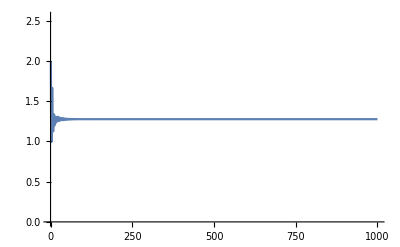

```mathematica
ListLinePlot[Table[L[k+1]/L[k],{k,1000}]]
```

```mathematica
Log[6]/Log[3]//N
```

1.63093

```mathematica
N[Log[6]/Log[3],20]
```

1.6309297535714574371